This is the function for the implicit form DAE.

```mathematica
F[ydot_,y1_,y2_,y3_,k_]:={
ydot-y2-y3,
y2+k y3-1,
y2 y3-y1/4
}
```

```mathematica
MatrixForm[F[ydot,y1,y2,y3,k]]
```

(-y2-y3+ydot
-1+y2+k y3
-y1/4+y2 y3)

The Jacobian is useful for determining which values of k will lead to "singularities".

```mathematica
Jac=D[F[ydot,y1,y2,y3,k],{{ydot,y2,y3}}]
```

{{1,-1,-1},{0,1,k},{0,y3,y2}}

```mathematica
MatrixForm[Jac]
```

(1 | -1 | -1
0 | 1 | k
0 | y3 | y2)

```mathematica
DetJac=Det[Jac]
```

y2-k y3

As can be seen from the above, it is advisable to avoid k=1.

Next, we try and solve for consistent initial conditions.

```mathematica
Sol1=Solve[{F[ydot,Subscript[y1, t0],y2,y3,k]==0},{ydot,y2,y3}]
```

{{ydot→1/2 (1+1/k+√(1-k y1_t0)-(√(1-k y1_t0))/k),y2→1/2+1/2 √(1-k y1_t0),y3→(1-√(1-k y1_t0))/(2 k)},{ydot→1/2+1/(2 k)-1/2 √(1-k y1_t0)+(√(1-k y1_t0))/(2 k),y2→1/2 (1-√(1-k y1_t0)),y3→(1+√(1-k y1_t0))/(2 k)}}

It's time to pick a value for k, remember to avoid k=1, so we choose k=-1.

```mathematica
Sol1/.k->-1/.Subscript[y1, t0]->1
```

{{ydot→√2,y2→1/2+1/(√2),y3→1/2 (-1+√2)},{ydot→-√2,y2→1/2 (1-√2),y3→1/2 (-1-√2)}}

Notice that there are 2 sets of initial conditions that will work.  This is not surprising, because the two algebraic equations are quadratic.

Double check the Jacobian that determines how the search for consistent initial conditions would behave.

```mathematica
DetJacGeneral=DetJac/.Sol1
```

{1/2+1/2 √(1-k y1_t0)+1/2 (-1+√(1-k y1_t0)),1/2 (-1-√(1-k y1_t0))+1/2 (1-√(1-k y1_t0))}

```mathematica
Simplify[DetJacGeneral/.k->-1/.Subscript[y1, t0]->1]
```

{√2,-√2}

```mathematica
N[%]
```

{1.41421,-1.41421}

Ok, let's try use the analytical Differential Equation solver to solve this DAE.

```mathematica
Sol2a=DSolve[
{
F[y1'[t],y1[t],y2[t],y3[t],k][[1]]==0,
F[y1'[t],y1[t],y2[t],y3[t],k][[2]]==0,
F[y1'[t],y1[t],y2[t],y3[t],k][[3]]==0,
y1[0]==1
}/.k->-1,
{y1[t],y2[t],y3[t]},t]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

DSolve[{-y2[t]-y3[t]+y1'[t]==0,-1+y2[t]-y3[t]==0,-y1[t]/4+y2[t] y3[t]==0,y1[0]==1},{y1[t],y2[t],y3[t]},t]

That didn't work for some reason.  Just to double check, let's write out the equations explicitly.

```mathematica
DSolve[
{
y1'[t]==y2[t]+y3[t],
y2[t]- y3[t]-1==0,
y2 [t]y3[t]-y1[t]/4==0,
y1[0]==1,
y2[0]==1/2 (1-√2),
y3[0]==1/2 (-1-√2)
},
{y1[t],y2[t],y3[t]},t
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

DSolve[{y1'[t]==y2[t]+y3[t],-1+y2[t]-y3[t]==0,-y1[t]/4+y2[t] y3[t]==0,y1[0]==1,y2[0]==1/2 (1-√2),y3[0]==1/2 (-1-√2)},{y1[t],y2[t],y3[t]},t]

Since DSolve is having trouble with the system expressed such that equations 2 and 3 are implicit, let's take the analytical-decoupled approach and first analytically solve the two algebraic equations.

```mathematica
Sol2=Solve[{
y2+k y3-1==0,
y2 y3-y1[t]/4==0
},
{y2,y3}
]
```

{{y2→1/2 (1-√(1-k y1[t])),y3→(1+√(1-k y1[t]))/(2 k)},{y2→1/2+1/2 √(1-k y1[t]),y3→(1-√(1-k y1[t]))/(2 k)}}

OK, let's try that in DSolve, one solution at a time.

```mathematica
Sol3a=DSolve[
{y1'[t]==y2+y3/.Sol2[[1]]/.k->-1,
y1[0]==1},
y1[t],t
]
```

{{y1[t]→1/4 (4-4 √2 t+t^2)},{y1[t]→1/4 (4+4 √2 t+t^2)}}

```mathematica
Sol3b=DSolve[
{y1'[t]==y2+y3/.Sol2[[2]]/.k->-1,
y1[0]==1},
y1[t],t
]
```

{{y1[t]→1/4 (4-4 √2 t+t^2)},{y1[t]→1/4 (4+4 √2 t+t^2)}}

OK, that worked.  Now let's compare that to a numerical solution.

```mathematica
Sol4=NDSolve[
{
F[y1'[t],y1[t],y2[t],y3[t],k][[1]]==0,
F[y1'[t],y1[t],y2[t],y3[t],k][[2]]==0,
F[y1'[t],y1[t],y2[t],y3[t],k][[3]]==0,
y1[0]==1
}/.k->-1,
{y1[t],y2[t],y3[t]},{t,0,100}]
```

{{y1[t]→InterpolatingFunction[{{0.,100.}},<>][t],y2[t]→InterpolatingFunction[{{0.,100.}},<>][t],y3[t]→InterpolatingFunction[{{0.,100.}},<>][t]}}

Ready to plot the results.

```mathematica
<<PlotLegends`
```

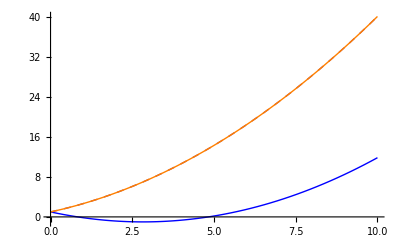

```mathematica
Plot[{
Evaluate[y1[t]/.Sol3b[[1]]],
Evaluate[y1[t]/.Sol3b[[2]]],
Evaluate[y1[t]/.Sol4]
},
{t,0,10},
PlotRange->All, 
PlotLegend->{"Analytical1","Analytical2", "Numerical"},
LegendPosition->{1.1,-0.4},
PlotStyle->{Blue,Directive[Thick,Dashed],Orange}]
```

That is quite satisfying, (especially when you don't just have the working finished product, but had to go through all that trial and error).  We now have a DAE with a known analytical solution.